# Метод на хордите

Задача: Дадено е уравенението:
x^2+  px − (q + 50) cos x − 2(p + q) = 0, където p и q са съответно предпоследната и последната цифра от факултетния ни номер (в случая p = 6 а q = 7)
x^2 + 6x − 57 cos x − 26 = 0
	 1.  Да се намери общия брой на корените на уравнението.
2. Да се локализира най-големия реален корен в интервала [a, b]. 
3. Да се проверят условията за приложение на метода на хордите.
		- проверка на сходимост
		- избор на начално приближение и постоянна точка
		- итерациите
	 4.  Да се изчисли корена по метода на хордите с точност 10^-4. Представете таблица с изчисленията.
	 5.  Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност.
6.  Да се направи сравнение кой метод е по-ефективен за избрания интервал.

```mathematica
f[x_] := x^2 +6x - 57 Cos[x] - 26
```

```mathematica
f[x]
```

-26+6 x+x^2-57 Cos[x]

## 1. Да се намери общия брой на корените на уравнението

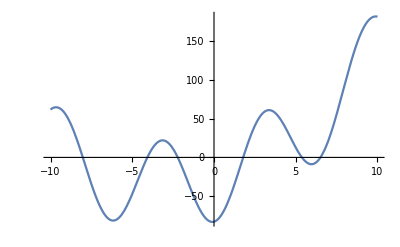

```mathematica
Plot[f[x], {x, -10, 10}]
```

Брой корени: 6

## 2. Да се локализира най-големия реален корен в интервала [a, b]

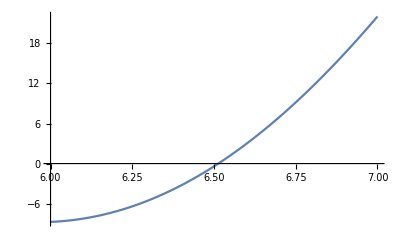

```mathematica
Plot[f[x], {x, 6, 7}]
```

```mathematica
f[6.]
```

-8.72971

```mathematica
f[7.]
```

22.0276

Извод:
(1) Функцията е непрекъсната, защото е сума от непрекъснати функции (полином и синус).
(2) f(5) = -8.729 ... < 0
       f(7) = 22.027 ... > 0
       => Функцията има различни знаци в двата края на разглеждания интервал [6; 7].
       От (1) и (2) следва, че функцията има поне един корен в разглеждания интервал [6; 7].

## 3. Да се проверят условията за приложение на метода на хордите

### Проверка на сходимост

#### Графика на първата производна

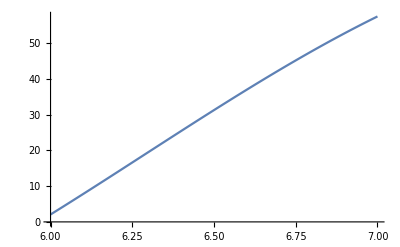

```mathematica
Plot[f'[x],{x,6,7}]
```

Извод: (1) Стойностите на първата производна в разглеждания интервал [5; 7] са между 2 и 60. Следователно първата f'(x) > 0 в целия разглеждан интервал [6; 7].

#### Графика на втората производна

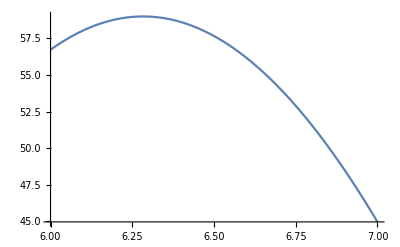

```mathematica
Plot[f''[x],{x,6,7}]
```

Извод : (2) Стойностите на втората производна в разглеждания интервал [6; 7] са между 56 и 45. Следователно втората f'' (x) > 0 в целия разглеждан интервал [5; 7] .

Извод: От (1) и (2) следва, че първата и втората производна имат постоянни знаци в разглеждания интервал [-6; -5]. Следователно условията за сходимост на метода на хордите са изпълнени.

### Избор на начално приближение и постоянна точка

Нужно е да е изпълнено условието f(x0).f’’(x) < 0
В нашия случай f’’(x) >0. Следователно е нужно f(x0) <0

```mathematica
p = 6.
```

6.

```mathematica
x0 = 7.
```

7.

### Итериране

```mathematica
For[n = 0, n <= 10, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1];
x0 = x1
]
```

n = 0 x_n = 6.28383

n = 1 x_n = 6.84878

n = 2 x_n = 6.32779

n = 3 x_n = 6.75421

n = 4 x_n = 6.36413

n = 5 x_n = 6.69054

n = 6 x_n = 6.39399

n = 7 x_n = 6.64574

n = 8 x_n = 6.41833

n = 9 x_n = 6.61332

n = 10 x_n = 6.43801

## 4. Да се изчисли корена по метода на хордите с точност 10^-4

### Изчисляване на постоянните величини

```mathematica
Plot[Abs[f'[x]],{x,6,7}]
```

-Graphics-

От геометрично съображение минимума на абсолютната стойност на първата производна се достига в левия край на интервала, а максимума - в десния.

```mathematica
M1 = Abs[f'[6.]]
```

2.07332

```mathematica
m1 = Abs[f'[7.]]
```

57.4482

```mathematica
R = (M1 - m1)/m1
```

-0.96391

```mathematica
f[x_] := x^2 +6x - 57 Cos[x] - 26
p = 6.; x0 = 7.;
M1 = Abs[f'[6.]];
m1 = Abs[f'[7.]];
R = (M1 - m1)/m1;
For[n = 0, n <= 10, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1, " f(x_n) = ", f[x1], " ε_n = ", eps = R * Abs[x1 - x0]];
x0 = x1
]
```

n = 0 x_n = 6.28383 f(x_n) = -5.81057 ε_n = -0.690327

n = 1 x_n = 6.84878 f(x_n) = 13.8752 ε_n = -0.544568

n = 2 x_n = 6.32779 f(x_n) = -4.93568 ε_n = -0.502192

n = 3 x_n = 6.75421 f(x_n) = 9.35173 ε_n = -0.411033

n = 4 x_n = 6.36413 f(x_n) = -4.12638 ε_n = -0.376

n = 5 x_n = 6.69054 f(x_n) = 6.57066 ε_n = -0.314625

n = 6 x_n = 6.39399 f(x_n) = -3.4034 ε_n = -0.285845

n = 7 x_n = 6.64574 f(x_n) = 4.74569 ε_n = -0.242665

n = 8 x_n = 6.41833 f(x_n) = -2.77539 ε_n = -0.219206

n = 9 x_n = 6.61332 f(x_n) = 3.49384 ε_n = -0.187951

n = 10 x_n = 6.43801 f(x_n) = -2.2421 ε_n = -0.168977

Цикъл със стоп-критерий при определена точност (в случая ε_n  = 0.0001)

```mathematica
f[x_]:=   x^2 +6x - 57 Cos[x] - 26
x0 = -5.; p = -6;
M1 = Abs[f'[6.]];
m1 = Abs[f'[7.]];
R = (M1 - m1)/m1;
epszad = 0.0001;
eps = 1;
Print["n = ",0,  " x_n = ", x0, " f(x_n) = ", f[x0]];
For[n = 1, eps > epszad, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1, " f(x_n) = ", f[x1], " ε_n = ", eps = R * Abs[x1 - x0]];
x0 = x1
]
```

n = 0 x_n = -5. f(x_n) = -47.1687

n = 1 x_n = -3.59454 f(x_n) = 16.6058 ε_n = -1.35474

## 5. Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност.

```mathematica
Log2[(7 - 6)/0.0001] - 1
```

12.2877

## 6. Да се направи сравнение кой метод е по-ефективен за избрания интервал

Извод: По метода на разполовяването биха били необходими 13 итерации за достигане на исканата точност. А по метода на хордите беше необходима само 1 итерация. Следователно методът на хордите е по-ефективен за избрания интервал [6, 7].